```mathematica
fileName = "/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json";
RadioButtonBar[
Dynamic[fileName],
{
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json",
"~/Downloads/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json
 | ~/Downloads/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
(*Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]*)
```

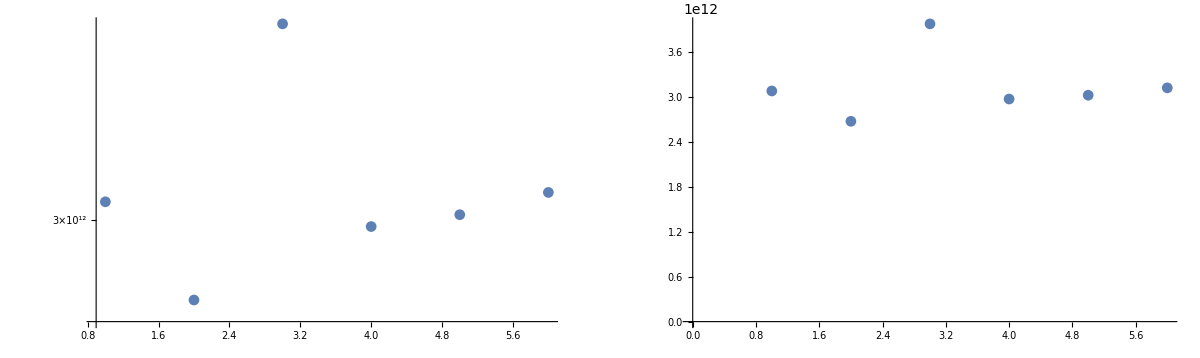

```mathematica
GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200]
```

### Live plot

```mathematica
(*Dynamic[livePlot]

makeLivePlot[]:=(
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];

livePlot = GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200];
)

task=CreateScheduledTask[makeLivePlot[],1]; (*Runs myFunction every 1 second*)
StartScheduledTask[task];*)
```

### Analyze

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]];
```

```mathematica
(*Format for yml*)
string = "";
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
];
string
```

L1PhaseSet : -21.5805783917
L2PhaseSet : -34.7982843414
S1EL_xOffset : 0.0000649855
S1EL_yOffset : 0.0001924621
S2EL_xOffset : 0.0000249194
S2EL_yOffset : 0.0000720062
S2ER_xOffset : -0.0000658789
S2ER_yOffset : -6.197e-7
S1ER_xOffset : 0.0000551462
S1ER_yOffset : 0.000142799
charge : 9.e-10
charge_nC : 0.86
PDrive_mean_x : 0.0002899709
PDrive_mean_y : -0.000035014
PDrive_sigma_x : 0.0002211439
PDrive_sigma_y : 0.0000979617
PDrive_mean_xp : -0.0000387019
PDrive_mean_yp : -1.1273e-6
PDrive_median_x : 0.000295055
PDrive_median_y : -0.0000372738
PDrive_median_xp : -0.000022774
PDrive_median_yp : -9.974e-7
PDrive_sigmaSI90_x : 0.0001990198
PDrive_sigmaSI90_y : 0.0000871767
PDrive_sigmaSI90_z : 0.0000530437
PDrive_emitSI90_x : 0.0000800058
PDrive_emitSI90_y : 4.0465e-6
PDrive_norm_emit_x : 0.0001093969
PDrive_norm_emit_y : 5.7192e-6
PDrive_zCentroid : 975.552720796
lostChargeFraction : 0.0002
errorTerm_lostChargeFraction : 0.
errorTerm_transverseOffset : 0.
errorTerm_angleOffset : 0.
errorTerm_mainObjective : 11.9749053459
errorTerm_secondaryObjective : 0.0127067249
maximizeMe : 3.9757454446863438e12
inputBeamFilePathSuffix : "/beams/2024-10-22_Impact_OneBunch/2024-10-22_oneBunch.h5"
csrTF : True

## Plot all

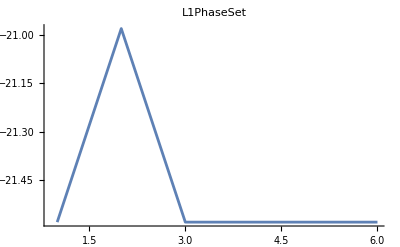
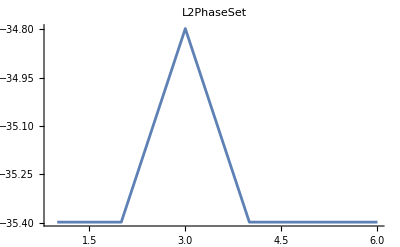
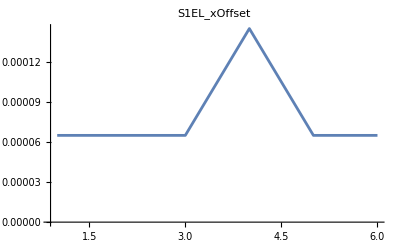
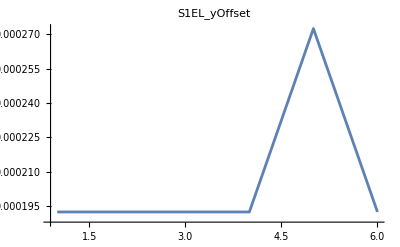
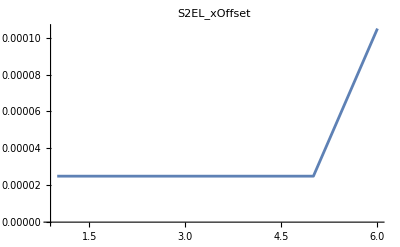
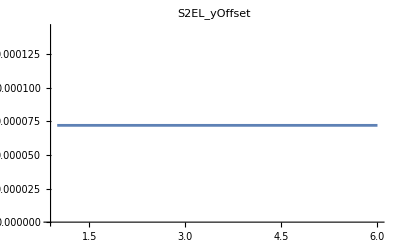
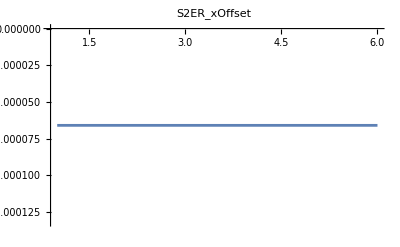
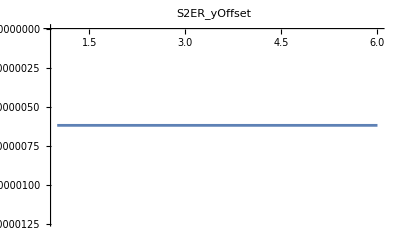
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 0

```mathematica
imgArr=Table[
ListPlot[
raw[[All,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"QA10361kG","QA10371kG","QE10425kG","QE10441kG","QE10511kG","QE10525kG","L0BPhaseSet","L1PhaseSet","L2PhaseSet","L3PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{L1PhaseSet,L2PhaseSet,S1EL_xOffset,S1EL_yOffset,S1ER_xOffset,S1ER_yOffset,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset}

```mathematica
fitVar = "PDrive_twiss_beta_x"
(*fitVar = "bunchSpacing"*)
```

PDrive_twiss_beta_x

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

LinearModelFit[{{-21.5806,-35.3983,0.0000649855,0.000192462,0.0000551462,0.000142799,0.0000249194,0.0000720062,-0.0000658789,-6.197×10^-7,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.9806,-35.3983,0.0000649855,0.000192462,0.0000551462,0.000142799,0.0000249194,0.0000720062,-0.0000658789,-6.197×10^-7,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-21.5806,-34.7983,0.0000649855,0.000192462,0.0000551462,0.000142799,0.0000249194,0.0000720062,-0.0000658789,-6.197×10^-7,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-21.5806,-35.3983,0.000144986,0.000192462,0.0000551462,0.000142799,0.0000249194,0.0000720062,-0.0000658789,-6.197×10^-7,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-21.5806,-35.3983,0.0000649855,0.000272462,0.0000551462,0.000142799,0.0000249194,0.0000720062,-0.0000658789,-6.197×10^-7,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-21.5806,-35.3983,0.0000649855,0.000192462,0.0000551462,0.000142799,0.000104919,0.0000720062,-0.0000658789,-6.197×10^-7,Missing[KeyAbsent,PDrive_twiss_beta_x]}},{L1PhaseSet,L2PhaseSet,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset},{L1PhaseSet,L2PhaseSet,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset}]

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

-Graphics-

```mathematica
lm["ANOVATable"]
```

LinearModelFit[{{-21.5806,-35.3983,0.0000649855,0.000192462,0.0000551462,0.000142799,0.0000249194,0.0000720062,-0.0000658789,-6.197×10^-7,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.9806,-35.3983,0.0000649855,0.000192462,0.0000551462,0.000142799,0.0000249194,0.0000720062,-0.0000658789,-6.197×10^-7,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-21.5806,-34.7983,0.0000649855,0.000192462,0.0000551462,0.000142799,0.0000249194,0.0000720062,-0.0000658789,-6.197×10^-7,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-21.5806,-35.3983,0.000144986,0.000192462,0.0000551462,0.000142799,0.0000249194,0.0000720062,-0.0000658789,-6.197×10^-7,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-21.5806,-35.3983,0.0000649855,0.000272462,0.0000551462,0.000142799,0.0000249194,0.0000720062,-0.0000658789,-6.197×10^-7,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-21.5806,-35.3983,0.0000649855,0.000192462,0.0000551462,0.000142799,0.000104919,0.0000720062,-0.0000658789,-6.197×10^-7,Missing[KeyAbsent,PDrive_twiss_beta_x]}},{L1PhaseSet,L2PhaseSet,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset},{L1PhaseSet,L2PhaseSet,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset}][ANOVATable]

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```

## Parse JSON strings to assoc

```mathematica
(*This is a stupid trick, but ensures numbers in scientific notation are interpreted correctly: https://mathematica.stackexchange.com/questions/15051/reading-in-scientific-notation-from-c-to-mathematica*)
stringToNumber[string_]:=ImportString[string,"Table"][[1,1]]
```

```mathematica
jsonTextToAssoc[string_]:=(
stringParts = StringSplit[StringDelete[#,WhitespaceCharacter],":"]&/@StringSplit[string,"\n"];
Association[#[[1]]->stringToNumber[#[[2]]]&/@stringParts]
)
```

```mathematica
tmp="L0BPhaseSet : -1.7210344516
L1PhaseSet : -20.3120443443
L2PhaseSet : -38.6737055166
L3PhaseSet : -1.4632882388
S1EL_xOffset : 0.0003852549
S1EL_yOffset : -0.0002411137
S2EL_xOffset : -0.0014178669
S2EL_yOffset : 0.0000111705
S2ER_xOffset : -0.002238162
S2ER_yOffset : -0.0006759962
S1ER_xOffset : 0.0010071369
S1ER_yOffset : 0.0003984557
XC1FFkG : 0.2064553639
XC3FFkG : -0.089916372
YC1FFkG : -0.0022311951
YC2FFkG : -0.0085115845";
```

```mathematica
priorSettings = jsonTextToAssoc[tmp]
```

<|L0BPhaseSet→-1.72103,L1PhaseSet→-20.312,L2PhaseSet→-38.6737,L3PhaseSet→-1.46329,S1EL_xOffset→0.000385255,S1EL_yOffset→-0.000241114,S2EL_xOffset→-0.00141787,S2EL_yOffset→0.0000111705,S2ER_xOffset→-0.00223816,S2ER_yOffset→-0.000675996,S1ER_xOffset→0.00100714,S1ER_yOffset→0.000398456,XC1FFkG→0.206455,XC3FFkG→-0.0899164,YC1FFkG→-0.0022312,YC2FFkG→-0.00851158|>

```mathematica
TableForm[
Table[
{
key,priorSettings[key],bestCase[key],bestCase[key]-priorSettings[key]
},
{key,Keys[priorSettings]}
],
TableHeadings->{None,{
Style["Parameter",Bold],
Style["150 μm spacing",Bold],
Style["New spacing",Bold],
Style["Delta",Bold]}}
]
```

Parameter | 150 μm spacing | New spacing | Delta
L0BPhaseSet | -1.72103 | Missing[KeyAbsent,L0BPhaseSet] | 1.72103+Missing[KeyAbsent,L0BPhaseSet]
L1PhaseSet | -20.312 | -21.5806 | -1.26853
L2PhaseSet | -38.6737 | -34.7983 | 3.87542
L3PhaseSet | -1.46329 | Missing[KeyAbsent,L3PhaseSet] | 1.46329+Missing[KeyAbsent,L3PhaseSet]
S1EL_xOffset | 0.000385255 | 0.0000649855 | -0.000320269
S1EL_yOffset | -0.000241114 | 0.000192462 | 0.000433576
S2EL_xOffset | -0.00141787 | 0.0000249194 | 0.00144279
S2EL_yOffset | 0.0000111705 | 0.0000720062 | 0.0000608357
S2ER_xOffset | -0.00223816 | -0.0000658789 | 0.00217228
S2ER_yOffset | -0.000675996 | -6.197×10^-7 | 0.000675377
S1ER_xOffset | 0.00100714 | 0.0000551462 | -0.000951991
S1ER_yOffset | 0.000398456 | 0.000142799 | -0.000255657
XC1FFkG | 0.206455 | Missing[KeyAbsent,XC1FFkG] | -0.206455+Missing[KeyAbsent,XC1FFkG]
XC3FFkG | -0.0899164 | Missing[KeyAbsent,XC3FFkG] | 0.0899164+Missing[KeyAbsent,XC3FFkG]
YC1FFkG | -0.0022312 | Missing[KeyAbsent,YC1FFkG] | 0.0022312+Missing[KeyAbsent,YC1FFkG]
YC2FFkG | -0.00851158 | Missing[KeyAbsent,YC2FFkG] | 0.00851158+Missing[KeyAbsent,YC2FFkG]

```mathematica
4
```

4